# Quiver scattering diagrams for local F0

```mathematica
SetDirectory[NotebookDirectory[]];
<<F0Scattering`
<<MaTeX`
```

F0Scattering 1.18, June 22, 2025 - A package for evaluating DT invariants on F0,F1

CoulombHiggs 6.3 - A package for evaluating quiver invariants

### Figure 3

```mathematica
(* orbifold scattering diagram for m=1/2, up to height 8, nL+nR<=4 at each intersection *)
ListRays=ConstructMcKayDiagram[8,1/2,{}];
```

Adding 28 rays,

Adding 84 rays,

Adding 92 rays,

Adding 60 rays,

Adding 4 rays,

272 in total.

```mathematica
(* in hidden cell below, rays with total height <=8, m=1/2 *)
```

```mathematica
ListRays={{{1,0,0,0},{21/4,1/4},0,0,0,0,1},{{0,1,0,0},{1/4,-21/4},0,0,0,0,1},{{0,0,1,0},{-21/4,-1/4},0,0,0,0,1},{{0,0,0,1},{-1/4,21/4},0,0,0,0,1},{{1,1,0,0},{1/4,1/4},1,2,1,1,2},{{1,2,0,0},{1/4,1/4},1,2,1,2,2},{{2,1,0,0},{1/4,1/4},1,2,2,1,2},{{2,3,0,0},{1/4,1/4},1,2,2,3,2},{{3,2,0,0},{1/4,1/4},1,2,3,2,2},{{3,4,0,0},{1/4,1/4},1,2,3,4,2},{{4,3,0,0},{1/4,1/4},1,2,4,3,2},{{1,0,0,1},{-1/4,1/4},1,4,1,1,2},{{1,0,0,2},{-1/4,1/4},1,4,1,2,2},{{2,0,0,1},{-1/4,1/4},1,4,2,1,2},{{2,0,0,3},{-1/4,1/4},1,4,2,3,2},{{3,0,0,2},{-1/4,1/4},1,4,3,2,2},{{3,0,0,4},{-1/4,1/4},1,4,3,4,2},{{4,0,0,3},{-1/4,1/4},1,4,4,3,2},{{0,1,1,0},{1/4,-1/4},2,3,1,1,2},{{0,1,2,0},{1/4,-1/4},2,3,1,2,2},{{0,2,1,0},{1/4,-1/4},2,3,2,1,2},{{0,2,3,0},{1/4,-1/4},2,3,2,3,2},{{0,3,2,0},{1/4,-1/4},2,3,3,2,2},{{0,3,4,0},{1/4,-1/4},2,3,3,4,2},{{0,4,3,0},{1/4,-1/4},2,3,4,3,2},{{0,0,1,1},{-1/4,-1/4},3,4,1,1,2},{{0,0,1,2},{-1/4,-1/4},3,4,1,2,2},{{0,0,2,1},{-1/4,-1/4},3,4,2,1,2},{{0,0,2,3},{-1/4,-1/4},3,4,2,3,2},{{0,0,3,2},{-1/4,-1/4},3,4,3,2,2},{{0,0,3,4},{-1/4,-1/4},3,4,3,4,2},{{0,0,4,3},{-1/4,-1/4},3,4,4,3,2},{{1,1,1,0},{3/4,1/4},1,19,1,1,3},{{1,2,2,0},{3/4,1/4},1,19,1,2,3},{{2,1,1,0},{3/4,1/4},1,19,2,1,3},{{2,3,3,0},{3/4,1/4},1,19,2,3,3},{{3,2,2,0},{3/4,1/4},1,19,3,2,3},{{1,1,2,0},{5/4,1/4},1,20,1,1,3},{{1,2,4,0},{5/4,1/4},1,20,1,2,3},{{2,1,2,0},{5/4,1/4},1,20,2,1,3},{{1,2,1,0},{1/2,1/4},1,21,1,1,3},{{1,4,2,0},{1/2,1/4},1,21,1,2,3},{{2,2,1,0},{1/2,1/4},1,21,2,1,3},{{3,2,1,0},{1/2,1/4},1,21,3,1,3},{{4,2,1,0},{1/2,1/4},1,21,4,1,3},{{1,2,3,0},{1,1/4},1,22,1,1,3},{{2,2,3,0},{1,1/4},1,22,2,1,3},{{3,2,3,0},{1,1/4},1,22,3,1,3},{{1,3,2,0},{7/12,1/4},1,23,1,1,3},{{2,3,2,0},{7/12,1/4},1,23,2,1,3},{{3,3,2,0},{7/12,1/4},1,23,3,1,3},{{1,3,4,0},{11/12,1/4},1,24,1,1,3},{{1,4,3,0},{5/8,1/4},1,25,1,1,3},{{0,1,1,1},{1/4,-3/4},2,26,1,1,3},{{0,1,2,2},{1/4,-3/4},2,26,1,2,3},{{0,2,1,1},{1/4,-3/4},2,26,2,1,3},{{0,2,3,3},{1/4,-3/4},2,26,2,3,3},{{0,3,2,2},{1/4,-3/4},2,26,3,2,3},{{0,1,1,2},{1/4,-5/4},2,27,1,1,3},{{0,1,2,4},{1/4,-5/4},2,27,1,2,3},{{0,2,1,2},{1/4,-5/4},2,27,2,1,3},{{0,1,2,1},{1/4,-1/2},2,28,1,1,3},{{0,1,4,2},{1/4,-1/2},2,28,1,2,3},{{0,2,2,1},{1/4,-1/2},2,28,2,1,3},{{0,3,2,1},{1/4,-1/2},2,28,3,1,3},{{0,4,2,1},{1/4,-1/2},2,28,4,1,3},{{0,1,2,3},{1/4,-1},2,29,1,1,3},{{0,2,2,3},{1/4,-1},2,29,2,1,3},{{0,3,2,3},{1/4,-1},2,29,3,1,3},{{0,1,3,2},{1/4,-7/12},2,30,1,1,3},{{0,2,3,2},{1/4,-7/12},2,30,2,1,3},{{0,3,3,2},{1/4,-7/12},2,30,3,1,3},{{0,1,3,4},{1/4,-11/12},2,31,1,1,3},{{0,1,4,3},{1/4,-5/8},2,32,1,1,3},{{1,0,1,1},{-3/4,-1/4},3,12,1,1,3},{{2,0,1,2},{-3/4,-1/4},3,12,1,2,3},{{1,0,2,1},{-3/4,-1/4},3,12,2,1,3},{{3,0,2,3},{-3/4,-1/4},3,12,2,3,3},{{2,0,3,2},{-3/4,-1/4},3,12,3,2,3},{{1,0,1,2},{-1/2,-1/4},3,13,1,1,3},{{2,0,1,4},{-1/2,-1/4},3,13,1,2,3},{{1,0,2,2},{-1/2,-1/4},3,13,2,1,3},{{1,0,3,2},{-1/2,-1/4},3,13,3,1,3},{{1,0,4,2},{-1/2,-1/4},3,13,4,1,3},{{2,0,1,1},{-5/4,-1/4},3,14,1,1,3},{{4,0,1,2},{-5/4,-1/4},3,14,1,2,3},{{2,0,2,1},{-5/4,-1/4},3,14,2,1,3},{{2,0,1,3},{-7/12,-1/4},3,15,1,1,3},{{2,0,2,3},{-7/12,-1/4},3,15,2,1,3},{{2,0,3,3},{-7/12,-1/4},3,15,3,1,3},{{3,0,1,2},{-1,-1/4},3,16,1,1,3},{{3,0,2,2},{-1,-1/4},3,16,2,1,3},{{3,0,3,2},{-1,-1/4},3,16,3,1,3},{{3,0,1,4},{-5/8,-1/4},3,17,1,1,3},{{4,0,1,3},{-11/12,-1/4},3,18,1,1,3},{{1,1,0,1},{-1/4,3/4},4,5,1,1,3},{{2,2,0,1},{-1/4,3/4},4,5,1,2,3},{{1,1,0,2},{-1/4,3/4},4,5,2,1,3},{{3,3,0,2},{-1/4,3/4},4,5,2,3,3},{{2,2,0,3},{-1/4,3/4},4,5,3,2,3},{{1,2,0,1},{-1/4,5/4},4,6,1,1,3},{{2,4,0,1},{-1/4,5/4},4,6,1,2,3},{{1,2,0,2},{-1/4,5/4},4,6,2,1,3},{{2,1,0,1},{-1/4,1/2},4,7,1,1,3},{{4,2,0,1},{-1/4,1/2},4,7,1,2,3},{{2,1,0,2},{-1/4,1/2},4,7,2,1,3},{{2,1,0,3},{-1/4,1/2},4,7,3,1,3},{{2,1,0,4},{-1/4,1/2},4,7,4,1,3},{{2,3,0,1},{-1/4,1},4,8,1,1,3},{{2,3,0,2},{-1/4,1},4,8,2,1,3},{{2,3,0,3},{-1/4,1},4,8,3,1,3},{{3,2,0,1},{-1/4,7/12},4,9,1,1,3},{{3,2,0,2},{-1/4,7/12},4,9,2,1,3},{{3,2,0,3},{-1/4,7/12},4,9,3,1,3},{{3,4,0,1},{-1/4,11/12},4,10,1,1,3},{{4,3,0,1},{-1/4,5/8},4,11,1,1,3},{{1,2,1,1},{5/4,1/4},1,56,1,1,4},{{2,2,1,1},{5/4,1/4},1,56,2,1,4},{{1,3,2,2},{9/4,1/4},1,58,1,1,4},{{1,2,2,1},{7/4,1/4},1,64,1,1,4},{{2,2,2,1},{7/4,1/4},1,64,2,1,4},{{1,3,2,1},{1,1/4},1,65,1,1,4},{{2,3,2,1},{1,1/4},1,65,2,1,4},{{1,4,2,1},{3/4,1/4},1,66,1,1,4},{{2,1,0,2},{-3/4,1/4},1,98,1,1,4},{{3,1,0,2},{-3/4,1/4},1,98,2,1,4},{{3,2,0,3},{-5/4,1/4},1,100,1,1,4},{{3,1,0,2},{-3/4,1/4},1,106,1,1,4},{{4,1,0,2},{-3/4,1/4},1,106,2,1,4},{{3,1,0,3},{-1/2,1/4},1,107,1,1,4},{{4,1,0,3},{-1/2,1/4},1,107,2,1,4},{{3,1,0,4},{-5/12,1/4},1,108,1,1,4},{{2,2,1,0},{1/4,3/4},2,35,1,1,4},{{2,3,1,0},{1/4,3/4},2,35,2,1,4},{{3,3,2,0},{1/4,5/4},2,37,1,1,4},{{2,3,1,0},{1/4,3/4},2,43,1,1,4},{{2,4,1,0},{1/4,3/4},2,43,2,1,4},{{3,3,1,0},{1/4,1/2},2,44,1,1,4},{{3,4,1,0},{1/4,1/2},2,44,2,1,4},{{4,3,1,0},{1/4,5/12},2,45,1,1,4},{{1,1,2,1},{1/4,-5/4},2,77,1,1,4},{{1,2,2,1},{1/4,-5/4},2,77,2,1,4},{{2,1,3,2},{1/4,-9/4},2,79,1,1,4},{{1,1,2,2},{1/4,-7/4},2,82,1,1,4},{{1,2,2,2},{1/4,-7/4},2,82,2,1,4},{{1,1,3,2},{1/4,-1},2,83,1,1,4},{{1,2,3,2},{1/4,-1},2,83,2,1,4},{{1,1,4,2},{1/4,-3/4},2,84,1,1,4},{{0,2,2,1},{3/4,-1/4},3,56,1,1,4},{{0,2,3,1},{3/4,-1/4},3,56,2,1,4},{{0,3,3,2},{5/4,-1/4},3,58,1,1,4},{{0,2,3,1},{3/4,-1/4},3,64,1,1,4},{{0,2,4,1},{3/4,-1/4},3,64,2,1,4},{{0,3,3,1},{1/2,-1/4},3,65,1,1,4},{{0,3,4,1},{1/2,-1/4},3,65,2,1,4},{{0,4,3,1},{5/12,-1/4},3,66,1,1,4},{{1,1,1,2},{-5/4,-1/4},3,98,1,1,4},{{1,1,2,2},{-5/4,-1/4},3,98,2,1,4},{{2,2,1,3},{-9/4,-1/4},3,100,1,1,4},{{2,1,1,2},{-7/4,-1/4},3,106,1,1,4},{{2,1,2,2},{-7/4,-1/4},3,106,2,1,4},{{2,1,1,3},{-1,-1/4},3,107,1,1,4},{{2,1,2,3},{-1,-1/4},3,107,2,1,4},{{2,1,1,4},{-3/4,-1/4},3,108,1,1,4},{{2,1,1,1},{-1/4,5/4},4,35,1,1,4},{{2,1,1,2},{-1/4,5/4},4,35,2,1,4},{{3,2,2,1},{-1/4,9/4},4,37,1,1,4},{{2,2,1,1},{-1/4,7/4},4,43,1,1,4},{{2,2,1,2},{-1/4,7/4},4,43,2,1,4},{{3,2,1,1},{-1/4,1},4,44,1,1,4},{{3,2,1,2},{-1/4,1},4,44,2,1,4},{{4,2,1,1},{-1/4,3/4},4,45,1,1,4},{{1,0,2,2},{-1/4,-3/4},4,77,1,1,4},{{1,0,2,3},{-1/4,-3/4},4,77,2,1,4},{{2,0,3,3},{-1/4,-5/4},4,79,1,1,4},{{1,0,2,3},{-1/4,-3/4},4,82,1,1,4},{{1,0,2,4},{-1/4,-3/4},4,82,2,1,4},{{1,0,3,3},{-1/4,-1/2},4,83,1,1,4},{{1,0,3,4},{-1/4,-1/2},4,83,2,1,4},{{1,0,4,3},{-1/4,-5/12},4,84,1,1,4},{{2,3,0,2},{-3/4,5/4},5,103,1,1,5},{{3,3,1,0},{-1/4,5/4},6,35,1,1,5},{{3,2,0,1},{-3/4,3/4},7,96,1,1,5},{{3,2,0,2},{-5/12,7/12},7,98,1,1,5},{{3,3,0,2},{-7/4,5/4},7,103,1,1,5},{{4,3,0,1},{-1/2,3/4},9,96,1,1,5},{{3,0,2,2},{-5/4,-3/4},12,87,1,1,5},{{2,0,1,3},{-3/4,-3/4},13,75,1,1,5},{{2,0,2,3},{-7/12,-5/12},13,77,1,1,5},{{3,0,2,3},{-5/4,-7/4},13,87,1,1,5},{{3,1,0,3},{-5/4,-1/4},14,98,1,1,5},{{3,0,1,4},{-3/4,-1/2},15,75,1,1,5},{{2,2,3,0},{5/4,3/4},19,40,1,1,5},{{0,3,3,1},{5/4,1/4},20,56,1,1,5},{{1,3,2,0},{3/4,3/4},21,33,1,1,5},{{2,3,2,0},{7/12,5/12},21,35,1,1,5},{{2,3,3,0},{5/4,7/4},21,40,1,1,5},{{1,4,3,0},{3/4,1/2},23,33,1,1,5},{{0,2,2,3},{3/4,-5/4},26,61,1,1,5},{{1,0,3,3},{1/4,-5/4},27,77,1,1,5},{{0,1,3,2},{3/4,-3/4},28,54,1,1,5},{{0,2,3,2},{5/12,-7/12},28,56,1,1,5},{{0,2,3,3},{7/4,-5/4},28,61,1,1,5},{{0,1,4,3},{1/2,-3/4},30,54,1,1,5},{{3,3,2,0},{1/2,1/2},35,41,1,1,6},{{0,3,3,2},{1/2,-1/2},56,62,1,1,6},{{2,0,3,3},{-1/2,-1/2},77,80,1,1,6},{{3,2,0,3},{-1/2,1/2},98,104,1,1,6},{{2,2,2,1},{7/4,1/4},1,142,1,1,5},{{3,2,2,1},{7/4,1/4},1,142,2,1,5},{{1,2,2,1},{7/4,1/4},1,149,1,1,5},{{2,2,2,1},{7/4,1/4},1,149,2,1,5},{{1,2,3,1},{9/4,1/4},1,150,1,1,5},{{2,2,3,1},{9/4,1/4},1,150,2,1,5},{{1,2,3,1},{9/4,1/4},1,152,1,1,5},{{2,2,3,1},{9/4,1/4},1,152,2,1,5},{{1,2,4,1},{11/4,1/4},1,153,1,1,5},{{1,3,3,1},{5/4,1/4},1,154,1,1,5},{{3,1,1,2},{-5/4,1/4},1,166,1,1,5},{{4,1,1,2},{-5/4,1/4},1,166,2,1,5},{{2,3,1,1},{1/4,5/4},2,118,1,1,5},{{2,4,1,1},{1/4,5/4},2,118,2,1,5},{{1,2,2,2},{1/4,-7/4},2,158,1,1,5},{{1,3,2,2},{1/4,-7/4},2,158,2,1,5},{{1,1,2,2},{1/4,-7/4},2,173,1,1,5},{{1,2,2,2},{1/4,-7/4},2,173,2,1,5},{{1,1,2,3},{1/4,-9/4},2,174,1,1,5},{{1,2,2,3},{1/4,-9/4},2,174,2,1,5},{{1,1,2,3},{1/4,-9/4},2,176,1,1,5},{{1,2,2,3},{1/4,-9/4},2,176,2,1,5},{{1,1,2,4},{1/4,-11/4},2,177,1,1,5},{{1,1,3,3},{1/4,-5/4},2,178,1,1,5},{{2,1,1,2},{-7/4,-1/4},3,125,1,1,5},{{2,1,2,2},{-7/4,-1/4},3,125,2,1,5},{{3,1,1,2},{-9/4,-1/4},3,126,1,1,5},{{3,1,2,2},{-9/4,-1/4},3,126,2,1,5},{{3,1,1,2},{-9/4,-1/4},3,128,1,1,5},{{3,1,2,2},{-9/4,-1/4},3,128,2,1,5},{{4,1,1,2},{-11/4,-1/4},3,129,1,1,5},{{3,1,1,3},{-5/4,-1/4},3,130,1,1,5},{{1,2,3,1},{5/4,-1/4},3,142,1,1,5},{{1,2,4,1},{5/4,-1/4},3,142,2,1,5},{{2,1,2,2},{-7/4,-1/4},3,166,1,1,5},{{2,1,3,2},{-7/4,-1/4},3,166,2,1,5},{{2,2,1,2},{-1/4,7/4},4,118,1,1,5},{{2,2,1,3},{-1/4,7/4},4,118,2,1,5},{{2,2,1,1},{-1/4,7/4},4,133,1,1,5},{{2,2,1,2},{-1/4,7/4},4,133,2,1,5},{{2,3,1,1},{-1/4,9/4},4,134,1,1,5},{{2,3,1,2},{-1/4,9/4},4,134,2,1,5},{{2,3,1,1},{-1/4,9/4},4,136,1,1,5},{{2,3,1,2},{-1/4,9/4},4,136,2,1,5},{{2,4,1,1},{-1/4,11/4},4,137,1,1,5},{{3,3,1,1},{-1/4,5/4},4,138,1,1,5},{{1,1,2,3},{-1/4,-5/4},4,158,1,1,5},{{1,1,2,4},{-1/4,-5/4},4,158,2,1,5},{{3,2,1,1},{-3/4,5/4},5,165,1,1,6},{{3,2,1,2},{-1/2,1},5,166,1,1,6},{{4,2,1,1},{-7/4,5/4},7,165,1,1,6},{{2,1,1,3},{-5/4,-3/4},12,157,1,1,6},{{2,1,2,3},{-1,-1/2},12,158,1,1,6},{{2,1,1,4},{-5/4,-7/4},13,157,1,1,6},{{1,3,2,1},{5/4,3/4},19,117,1,1,6},{{2,3,2,1},{1,1/2},19,118,1,1,6},{{1,4,2,1},{5/4,7/4},21,117,1,1,6},{{1,1,3,2},{3/4,-5/4},26,141,1,1,6},{{1,2,3,2},{1/2,-1},26,142,1,1,6},{{1,1,4,2},{7/4,-5/4},28,141,1,1,6},{{2,2,3,1},{9/4,1/4},1,241,1,1,6},{{1,2,2,3},{1/4,-9/4},2,255,1,1,6},{{3,1,2,2},{-9/4,-1/4},3,219,1,1,6},{{2,3,1,2},{-1/4,9/4},4,221,1,1,6}};
```

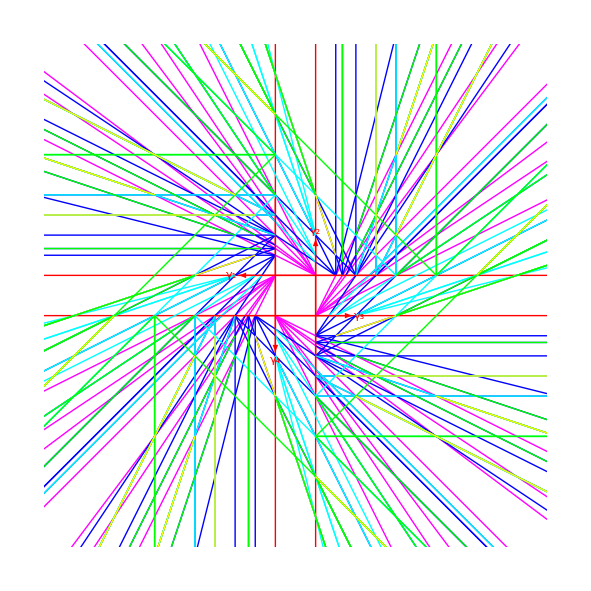

```mathematica
Gr=With[{L=3,m=1/2},Show[Graphics[Table[{Hue[1-(ListRays[[k,7]]-1)/6],McKayRay[ListRays[[k,1]],ListRays[[k,2]],{0,25},""]},{k,Length[ListRays]}]],McKayInitialRays[.95,m],PlotRange->{{-L,L},{-L,L}}]]
```

{{2 γ_2,{2 γ_3,{γ_1,γ_4}}},{γ_1,{2 γ_2,{2 γ_3,γ_4}}},{γ_1,{γ_3,{2 γ_2,{γ_3,γ_4}}}}}

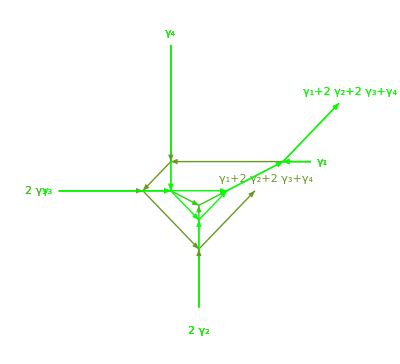

-y^5-3 y^3-7 y+O[1/y]^1

```mathematica
(* find scattering sequences corresponding to given dimension vector *)
With[{Nvec={1,2,2,1},m=1/2},
LiTrees=McKayTreesFromListRays[ListRays,Nvec,m];
Print[LiTrees/.McKayrep];
Print[McKayScattDiag[LiTrees,m]];
Index=McKayScattIndexImproved[LiTrees];
Plus@@Series[EvaluateKronecker[Index],{y,Infinity,0}]
]
```

### Figure 21

```mathematica
(* orbifold scattering diagram for m=1/2, up to height 8, nL+nR<=4 at each intersection *)
ListRays=ConstructMcKayDiagram[8,1/4,{}];
```

```mathematica
(* in hidden cell below, rays with total height <=8, m=1/4 *)
```

```mathematica
ListRays={{{1,0,0,0},{41/8,3/8},0,0,0,0,1},{{0,1,0,0},{1/8,-43/8},0,0,0,0,1},{{0,0,1,0},{-41/8,-3/8},0,0,0,0,1},{{0,0,0,1},{-1/8,43/8},0,0,0,0,1},{{1,1,0,0},{1/8,3/8},1,2,1,1,2},{{1,2,0,0},{1/8,3/8},1,2,1,2,2},{{2,1,0,0},{1/8,3/8},1,2,2,1,2},{{2,3,0,0},{1/8,3/8},1,2,2,3,2},{{3,2,0,0},{1/8,3/8},1,2,3,2,2},{{3,4,0,0},{1/8,3/8},1,2,3,4,2},{{4,3,0,0},{1/8,3/8},1,2,4,3,2},{{1,0,0,1},{-1/8,3/8},1,4,1,1,2},{{1,0,0,2},{-1/8,3/8},1,4,1,2,2},{{2,0,0,1},{-1/8,3/8},1,4,2,1,2},{{2,0,0,3},{-1/8,3/8},1,4,2,3,2},{{3,0,0,2},{-1/8,3/8},1,4,3,2,2},{{3,0,0,4},{-1/8,3/8},1,4,3,4,2},{{4,0,0,3},{-1/8,3/8},1,4,4,3,2},{{0,1,1,0},{1/8,-3/8},2,3,1,1,2},{{0,1,2,0},{1/8,-3/8},2,3,1,2,2},{{0,2,1,0},{1/8,-3/8},2,3,2,1,2},{{0,2,3,0},{1/8,-3/8},2,3,2,3,2},{{0,3,2,0},{1/8,-3/8},2,3,3,2,2},{{0,3,4,0},{1/8,-3/8},2,3,3,4,2},{{0,4,3,0},{1/8,-3/8},2,3,4,3,2},{{0,0,1,1},{-1/8,-3/8},3,4,1,1,2},{{0,0,1,2},{-1/8,-3/8},3,4,1,2,2},{{0,0,2,1},{-1/8,-3/8},3,4,2,1,2},{{0,0,2,3},{-1/8,-3/8},3,4,2,3,2},{{0,0,3,2},{-1/8,-3/8},3,4,3,2,2},{{0,0,3,4},{-1/8,-3/8},3,4,3,4,2},{{0,0,4,3},{-1/8,-3/8},3,4,4,3,2},{{1,1,1,0},{7/8,3/8},1,19,1,1,3},{{1,2,2,0},{7/8,3/8},1,19,1,2,3},{{2,1,1,0},{7/8,3/8},1,19,2,1,3},{{2,3,3,0},{7/8,3/8},1,19,2,3,3},{{3,2,2,0},{7/8,3/8},1,19,3,2,3},{{1,1,2,0},{13/8,3/8},1,20,1,1,3},{{1,2,4,0},{13/8,3/8},1,20,1,2,3},{{2,1,2,0},{13/8,3/8},1,20,2,1,3},{{1,2,1,0},{1/2,3/8},1,21,1,1,3},{{1,4,2,0},{1/2,3/8},1,21,1,2,3},{{2,2,1,0},{1/2,3/8},1,21,2,1,3},{{3,2,1,0},{1/2,3/8},1,21,3,1,3},{{4,2,1,0},{1/2,3/8},1,21,4,1,3},{{1,2,3,0},{5/4,3/8},1,22,1,1,3},{{2,2,3,0},{5/4,3/8},1,22,2,1,3},{{3,2,3,0},{5/4,3/8},1,22,3,1,3},{{1,3,2,0},{5/8,3/8},1,23,1,1,3},{{2,3,2,0},{5/8,3/8},1,23,2,1,3},{{3,3,2,0},{5/8,3/8},1,23,3,1,3},{{1,3,4,0},{9/8,3/8},1,24,1,1,3},{{1,4,3,0},{11/16,3/8},1,25,1,1,3},{{0,1,1,1},{1/8,-5/8},2,26,1,1,3},{{0,1,2,2},{1/8,-5/8},2,26,1,2,3},{{0,2,1,1},{1/8,-5/8},2,26,2,1,3},{{0,2,3,3},{1/8,-5/8},2,26,2,3,3},{{0,3,2,2},{1/8,-5/8},2,26,3,2,3},{{0,1,1,2},{1/8,-7/8},2,27,1,1,3},{{0,1,2,4},{1/8,-7/8},2,27,1,2,3},{{0,2,1,2},{1/8,-7/8},2,27,2,1,3},{{0,1,2,1},{1/8,-1/2},2,28,1,1,3},{{0,1,4,2},{1/8,-1/2},2,28,1,2,3},{{0,2,2,1},{1/8,-1/2},2,28,2,1,3},{{0,3,2,1},{1/8,-1/2},2,28,3,1,3},{{0,4,2,1},{1/8,-1/2},2,28,4,1,3},{{0,1,2,3},{1/8,-3/4},2,29,1,1,3},{{0,2,2,3},{1/8,-3/4},2,29,2,1,3},{{0,3,2,3},{1/8,-3/4},2,29,3,1,3},{{0,1,3,2},{1/8,-13/24},2,30,1,1,3},{{0,2,3,2},{1/8,-13/24},2,30,2,1,3},{{0,3,3,2},{1/8,-13/24},2,30,3,1,3},{{0,1,3,4},{1/8,-17/24},2,31,1,1,3},{{0,1,4,3},{1/8,-9/16},2,32,1,1,3},{{1,0,1,1},{-7/8,-3/8},3,12,1,1,3},{{2,0,1,2},{-7/8,-3/8},3,12,1,2,3},{{1,0,2,1},{-7/8,-3/8},3,12,2,1,3},{{3,0,2,3},{-7/8,-3/8},3,12,2,3,3},{{2,0,3,2},{-7/8,-3/8},3,12,3,2,3},{{1,0,1,2},{-1/2,-3/8},3,13,1,1,3},{{2,0,1,4},{-1/2,-3/8},3,13,1,2,3},{{1,0,2,2},{-1/2,-3/8},3,13,2,1,3},{{1,0,3,2},{-1/2,-3/8},3,13,3,1,3},{{1,0,4,2},{-1/2,-3/8},3,13,4,1,3},{{2,0,1,1},{-13/8,-3/8},3,14,1,1,3},{{4,0,1,2},{-13/8,-3/8},3,14,1,2,3},{{2,0,2,1},{-13/8,-3/8},3,14,2,1,3},{{2,0,1,3},{-5/8,-3/8},3,15,1,1,3},{{2,0,2,3},{-5/8,-3/8},3,15,2,1,3},{{2,0,3,3},{-5/8,-3/8},3,15,3,1,3},{{3,0,1,2},{-5/4,-3/8},3,16,1,1,3},{{3,0,2,2},{-5/4,-3/8},3,16,2,1,3},{{3,0,3,2},{-5/4,-3/8},3,16,3,1,3},{{3,0,1,4},{-11/16,-3/8},3,17,1,1,3},{{4,0,1,3},{-9/8,-3/8},3,18,1,1,3},{{1,1,0,1},{-1/8,5/8},4,5,1,1,3},{{2,2,0,1},{-1/8,5/8},4,5,1,2,3},{{1,1,0,2},{-1/8,5/8},4,5,2,1,3},{{3,3,0,2},{-1/8,5/8},4,5,2,3,3},{{2,2,0,3},{-1/8,5/8},4,5,3,2,3},{{1,2,0,1},{-1/8,7/8},4,6,1,1,3},{{2,4,0,1},{-1/8,7/8},4,6,1,2,3},{{1,2,0,2},{-1/8,7/8},4,6,2,1,3},{{2,1,0,1},{-1/8,1/2},4,7,1,1,3},{{4,2,0,1},{-1/8,1/2},4,7,1,2,3},{{2,1,0,2},{-1/8,1/2},4,7,2,1,3},{{2,1,0,3},{-1/8,1/2},4,7,3,1,3},{{2,1,0,4},{-1/8,1/2},4,7,4,1,3},{{2,3,0,1},{-1/8,3/4},4,8,1,1,3},{{2,3,0,2},{-1/8,3/4},4,8,2,1,3},{{2,3,0,3},{-1/8,3/4},4,8,3,1,3},{{3,2,0,1},{-1/8,13/24},4,9,1,1,3},{{3,2,0,2},{-1/8,13/24},4,9,2,1,3},{{3,2,0,3},{-1/8,13/24},4,9,3,1,3},{{3,4,0,1},{-1/8,17/24},4,10,1,1,3},{{4,3,0,1},{-1/8,9/16},4,11,1,1,3},{{1,2,1,1},{9/8,3/8},1,56,1,1,4},{{2,2,1,1},{9/8,3/8},1,56,2,1,4},{{1,3,2,2},{17/8,3/8},1,58,1,1,4},{{1,2,2,1},{15/8,3/8},1,64,1,1,4},{{2,2,2,1},{15/8,3/8},1,64,2,1,4},{{1,3,2,1},{1,3/8},1,65,1,1,4},{{2,3,2,1},{1,3/8},1,65,2,1,4},{{1,4,2,1},{17/24,3/8},1,66,1,1,4},{{2,1,0,2},{-3/8,3/8},1,98,1,1,4},{{3,1,0,2},{-3/8,3/8},1,98,2,1,4},{{3,2,0,3},{-5/8,3/8},1,100,1,1,4},{{3,1,0,2},{-3/8,3/8},1,106,1,1,4},{{4,1,0,2},{-3/8,3/8},1,106,2,1,4},{{3,1,0,3},{-1/4,3/8},1,107,1,1,4},{{4,1,0,3},{-1/4,3/8},1,107,2,1,4},{{3,1,0,4},{-5/24,3/8},1,108,1,1,4},{{2,2,1,0},{1/8,9/8},2,35,1,1,4},{{2,3,1,0},{1/8,9/8},2,35,2,1,4},{{3,3,2,0},{1/8,15/8},2,37,1,1,4},{{2,3,1,0},{1/8,9/8},2,43,1,1,4},{{2,4,1,0},{1/8,9/8},2,43,2,1,4},{{3,3,1,0},{1/8,3/4},2,44,1,1,4},{{3,4,1,0},{1/8,3/4},2,44,2,1,4},{{4,3,1,0},{1/8,5/8},2,45,1,1,4},{{1,1,2,1},{1/8,-11/8},2,77,1,1,4},{{1,2,2,1},{1/8,-11/8},2,77,2,1,4},{{2,1,3,2},{1/8,-19/8},2,79,1,1,4},{{1,1,2,2},{1/8,-13/8},2,82,1,1,4},{{1,2,2,2},{1/8,-13/8},2,82,2,1,4},{{1,1,3,2},{1/8,-1},2,83,1,1,4},{{1,2,3,2},{1/8,-1},2,83,2,1,4},{{1,1,4,2},{1/8,-19/24},2,84,1,1,4},{{0,2,2,1},{3/8,-3/8},3,56,1,1,4},{{0,2,3,1},{3/8,-3/8},3,56,2,1,4},{{0,3,3,2},{5/8,-3/8},3,58,1,1,4},{{0,2,3,1},{3/8,-3/8},3,64,1,1,4},{{0,2,4,1},{3/8,-3/8},3,64,2,1,4},{{0,3,3,1},{1/4,-3/8},3,65,1,1,4},{{0,3,4,1},{1/4,-3/8},3,65,2,1,4},{{0,4,3,1},{5/24,-3/8},3,66,1,1,4},{{1,1,1,2},{-9/8,-3/8},3,98,1,1,4},{{1,1,2,2},{-9/8,-3/8},3,98,2,1,4},{{2,2,1,3},{-17/8,-3/8},3,100,1,1,4},{{2,1,1,2},{-15/8,-3/8},3,106,1,1,4},{{2,1,2,2},{-15/8,-3/8},3,106,2,1,4},{{2,1,1,3},{-1,-3/8},3,107,1,1,4},{{2,1,2,3},{-1,-3/8},3,107,2,1,4},{{2,1,1,4},{-17/24,-3/8},3,108,1,1,4},{{2,1,1,1},{-1/8,11/8},4,35,1,1,4},{{2,1,1,2},{-1/8,11/8},4,35,2,1,4},{{3,2,2,1},{-1/8,19/8},4,37,1,1,4},{{2,2,1,1},{-1/8,13/8},4,43,1,1,4},{{2,2,1,2},{-1/8,13/8},4,43,2,1,4},{{3,2,1,1},{-1/8,1},4,44,1,1,4},{{3,2,1,2},{-1/8,1},4,44,2,1,4},{{4,2,1,1},{-1/8,19/24},4,45,1,1,4},{{1,0,2,2},{-1/8,-9/8},4,77,1,1,4},{{1,0,2,3},{-1/8,-9/8},4,77,2,1,4},{{2,0,3,3},{-1/8,-15/8},4,79,1,1,4},{{1,0,2,3},{-1/8,-9/8},4,82,1,1,4},{{1,0,2,4},{-1/8,-9/8},4,82,2,1,4},{{1,0,3,3},{-1/8,-3/4},4,83,1,1,4},{{1,0,3,4},{-1/8,-3/4},4,83,2,1,4},{{1,0,4,3},{-1/8,-5/8},4,84,1,1,4},{{2,3,0,2},{-3/8,7/8},5,103,1,1,5},{{3,3,1,0},{-5/8,15/8},6,35,1,1,5},{{3,2,0,1},{-3/8,5/8},7,96,1,1,5},{{3,2,0,2},{-5/24,13/24},7,98,1,1,5},{{3,3,0,2},{-7/8,7/8},7,103,1,1,5},{{4,3,0,1},{-1/4,5/8},9,96,1,1,5},{{3,0,2,2},{-13/8,-9/8},12,87,1,1,5},{{2,0,1,3},{-7/8,-9/8},13,75,1,1,5},{{2,0,2,3},{-5/8,-5/8},13,77,1,1,5},{{3,0,2,3},{-13/8,-21/8},13,87,1,1,5},{{3,1,0,3},{-5/8,1/8},14,98,1,1,5},{{3,0,1,4},{-7/8,-3/4},15,75,1,1,5},{{2,2,3,0},{13/8,9/8},19,40,1,1,5},{{0,3,3,1},{5/8,-1/8},20,56,1,1,5},{{1,3,2,0},{7/8,9/8},21,33,1,1,5},{{2,3,2,0},{5/8,5/8},21,35,1,1,5},{{2,3,3,0},{13/8,21/8},21,40,1,1,5},{{1,4,3,0},{7/8,3/4},23,33,1,1,5},{{0,2,2,3},{3/8,-7/8},26,61,1,1,5},{{1,0,3,3},{5/8,-15/8},27,77,1,1,5},{{0,1,3,2},{3/8,-5/8},28,54,1,1,5},{{0,2,3,2},{5/24,-13/24},28,56,1,1,5},{{0,2,3,3},{7/8,-7/8},28,61,1,1,5},{{0,1,4,3},{1/4,-5/8},30,54,1,1,5},{{3,3,2,0},{1/2,3/4},35,41,1,1,6},{{0,3,3,2},{1/4,-1/2},56,62,1,1,6},{{2,0,3,3},{-1/2,-3/4},77,80,1,1,6},{{3,2,0,3},{-1/4,1/2},98,104,1,1,6},{{2,2,2,1},{15/8,3/8},1,142,1,1,5},{{3,2,2,1},{15/8,3/8},1,142,2,1,5},{{1,2,2,1},{15/8,3/8},1,149,1,1,5},{{2,2,2,1},{15/8,3/8},1,149,2,1,5},{{1,2,3,1},{21/8,3/8},1,150,1,1,5},{{2,2,3,1},{21/8,3/8},1,150,2,1,5},{{1,2,3,1},{21/8,3/8},1,152,1,1,5},{{2,2,3,1},{21/8,3/8},1,152,2,1,5},{{1,2,4,1},{27/8,3/8},1,153,1,1,5},{{1,3,3,1},{11/8,3/8},1,154,1,1,5},{{3,1,1,2},{-9/8,3/8},1,166,1,1,5},{{4,1,1,2},{-9/8,3/8},1,166,2,1,5},{{1,3,3,1},{11/8,3/8},1,194,1,1,6},{{2,3,1,1},{1/8,11/8},2,118,1,1,5},{{2,4,1,1},{1/8,11/8},2,118,2,1,5},{{1,2,2,2},{1/8,-13/8},2,158,1,1,5},{{1,3,2,2},{1/8,-13/8},2,158,2,1,5},{{1,1,2,2},{1/8,-13/8},2,173,1,1,5},{{1,2,2,2},{1/8,-13/8},2,173,2,1,5},{{1,1,2,3},{1/8,-15/8},2,174,1,1,5},{{1,2,2,3},{1/8,-15/8},2,174,2,1,5},{{1,1,2,3},{1/8,-15/8},2,176,1,1,5},{{1,2,2,3},{1/8,-15/8},2,176,2,1,5},{{1,1,2,4},{1/8,-17/8},2,177,1,1,5},{{1,1,3,3},{1/8,-9/8},2,178,1,1,5},{{2,1,1,2},{-15/8,-3/8},3,125,1,1,5},{{2,1,2,2},{-15/8,-3/8},3,125,2,1,5},{{3,1,1,2},{-21/8,-3/8},3,126,1,1,5},{{3,1,2,2},{-21/8,-3/8},3,126,2,1,5},{{3,1,1,2},{-21/8,-3/8},3,128,1,1,5},{{3,1,2,2},{-21/8,-3/8},3,128,2,1,5},{{4,1,1,2},{-27/8,-3/8},3,129,1,1,5},{{3,1,1,3},{-11/8,-3/8},3,130,1,1,5},{{1,2,3,1},{9/8,-3/8},3,142,1,1,5},{{1,2,4,1},{9/8,-3/8},3,142,2,1,5},{{2,1,2,2},{-15/8,-3/8},3,166,1,1,5},{{2,1,3,2},{-15/8,-3/8},3,166,2,1,5},{{3,1,1,3},{-11/8,-3/8},3,191,1,1,6},{{2,2,1,2},{-1/8,13/8},4,118,1,1,5},{{2,2,1,3},{-1/8,13/8},4,118,2,1,5},{{2,2,1,1},{-1/8,13/8},4,133,1,1,5},{{2,2,1,2},{-1/8,13/8},4,133,2,1,5},{{2,3,1,1},{-1/8,15/8},4,134,1,1,5},{{2,3,1,2},{-1/8,15/8},4,134,2,1,5},{{2,3,1,1},{-1/8,15/8},4,136,1,1,5},{{2,3,1,2},{-1/8,15/8},4,136,2,1,5},{{2,4,1,1},{-1/8,17/8},4,137,1,1,5},{{3,3,1,1},{-1/8,9/8},4,138,1,1,5},{{1,1,2,3},{-1/8,-11/8},4,158,1,1,5},{{1,1,2,4},{-1/8,-11/8},4,158,2,1,5},{{3,2,1,1},{-7/8,11/8},5,165,1,1,6},{{3,2,1,2},{-1/2,1},5,166,1,1,6},{{3,3,1,1},{-3/8,11/8},6,165,1,1,6},{{4,2,1,1},{-15/8,11/8},7,165,1,1,6},{{2,1,1,3},{-9/8,-5/8},12,157,1,1,6},{{2,1,2,3},{-1,-1/2},12,158,1,1,6},{{2,1,1,4},{-9/8,-13/8},13,157,1,1,6},{{1,3,2,1},{9/8,5/8},19,117,1,1,6},{{2,3,2,1},{1,1/2},19,118,1,1,6},{{1,4,2,1},{9/8,13/8},21,117,1,1,6},{{1,1,3,2},{7/8,-11/8},26,141,1,1,6},{{1,2,3,2},{1/2,-1},26,142,1,1,6},{{1,1,3,3},{3/8,-11/8},27,141,1,1,6},{{1,1,4,2},{15/8,-11/8},28,141,1,1,6},{{2,2,3,1},{21/8,3/8},1,242,1,1,6},{{1,2,2,3},{1/8,-15/8},2,257,1,1,6},{{3,1,2,2},{-21/8,-3/8},3,219,1,1,6},{{2,3,1,2},{-1/8,15/8},4,222,1,1,6}};
```

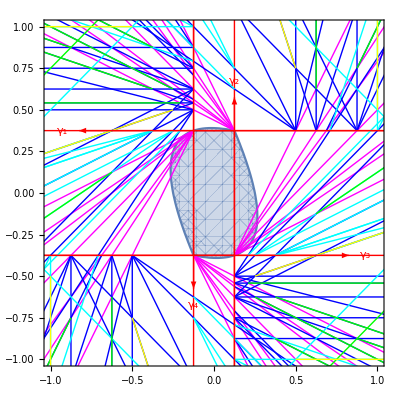

```mathematica
With[{L=1,m=1/4},Gr=Show[Graphics[Table[{Hue[1-(ListRays[[k,7]]-1)/6],McKayRay[ListRays[[k,1]],ListRays[[k,2]],{0,25},""]},{k,Length[ListRays]}]],McKayInitialRays[.95,m],PlotRange->{{-L,L},{-L,L}}];
Show[RegionPlot[(-1/4+u-m u+u^2-m v+2 u v+v^2<0)&&(-1/4-u+m u+u^2+m v+2 u v+v^2<0),{u,-1,1},{v,-1,1}],Gr]]
```

### Figure 21: scattering diagram for phase I quiver

```mathematica
(* for this one must changing temporarily the code in F0Scattering.m *)
```

```mathematica
MatI={{0,2,2,-4},{-2,0,0,2},{-2,0,0,2},{4,-2,-2,0}};
McKayDSZ[Nvec_,NNvec_]:=Tr[{Nvec}.MatI.Transpose[{NNvec}]];
McKayVec[Nvec_]:={-Nvec[[1]]+Nvec[[4]],Nvec[[2]]+Nvec[[3]]-2Nvec[[4]]};
McKayRayEq[{n1_,n2_,n3_,n4_},{u_,v_},m_]:=(-n3+2 n4) (-(m/2)-u)+n2 (-(m/2)+u)+n4 (1/2 (-1+m)-v)+n1 (1/2 (-1+m)+v);
McKayDSZ[{n1_,n2_,n3_,n4_},{nn1_,nn2_,nn3_,nn4_}]:=-2 n2 nn1-2 n3 nn1+4 n4 nn1+2 n1 nn2-2 n4 nn2+2 n1 nn3-2 n4 nn3-4 n1 nn4+2 n2 nn4+2 n3 nn4;
McKayIntersectRays[{n1_,n2_,n3_,n4_},{nn1_,nn2_,nn3_,nn4_},m_]:=If[-2 n2 nn1-2 n3 nn1+4 n4 nn1+2 n1 nn2-2 n4 nn2+2 n1 nn3-2 n4 nn3-4 n1 nn4+2 n2 nn4+2 n3 nn4==0,{},{(-2 n4 nn1+2 n1 nn4+m ((n1-n4) (nn2-nn3)+n3 (nn1-nn4)+n2 (-nn1+nn4)))/(2 (2 n4 nn1+n1 nn2-n4 nn2+n1 nn3-n4 nn3-2 n1 nn4+n2 (-nn1+nn4)+n3 (-nn1+nn4))),(-((-1+m) (n1+n4) (nn2+nn3-2 nn4))+n2 ((-1+m) nn1+2 m nn3-nn4-3 m nn4)+(-n3+2 n4) (nn1-m nn1+2 m nn2+nn4-m nn4))/(2 ((n1-n4) (nn2+nn3-2 nn4)-(n3-2 n4) (nn1-nn4)+n2 (-nn1+nn4)))}];
InitialRaysOrigin[m_]:={{m/2,(1-m)/2},{m/2,1/2 (-1-3 m)},{-(m/2),1/2 (-1+m)},{-(1/2),(1-m)/2}};
```

```mathematica
ListRaysI=ConstructMcKayDiagram[9,1/2,{}];
```

Adding 39 rays,

Adding 168 rays,

Adding 320 rays,

Adding 219 rays,

Adding 56 rays,

806 in total.

```mathematica
(* result stored in hidden cell below: rays with Nmax=9, m=1/2*)
```

```mathematica
ListRaysI={{{1,0,0,0},{21/4,1/4},0,0,0,0,1},{{0,1,0,0},{1/4,-25/4},0,0,0,0,1},{{0,0,1,0},{-1/4,-21/4},0,0,0,0,1},{{0,0,0,1},{-11/2,41/4},0,0,0,0,1},{{1,1,0,0},{1/4,1/4},1,2,1,1,2},{{1,2,0,0},{1/4,1/4},1,2,1,2,2},{{2,1,0,0},{1/4,1/4},1,2,2,1,2},{{2,3,0,0},{1/4,1/4},1,2,2,3,2},{{3,2,0,0},{1/4,1/4},1,2,3,2,2},{{3,4,0,0},{1/4,1/4},1,2,3,4,2},{{4,3,0,0},{1/4,1/4},1,2,4,3,2},{{1,0,1,0},{-1/4,1/4},1,3,1,1,2},{{1,0,2,0},{-1/4,1/4},1,3,1,2,2},{{2,0,1,0},{-1/4,1/4},1,3,2,1,2},{{2,0,3,0},{-1/4,1/4},1,3,2,3,2},{{3,0,2,0},{-1/4,1/4},1,3,3,2,2},{{3,0,4,0},{-1/4,1/4},1,3,3,4,2},{{4,0,3,0},{-1/4,1/4},1,3,4,3,2},{{1,0,0,1},{-1/2,1/4},1,4,1,1,2},{{1,0,0,2},{-1/2,1/4},1,4,1,2,2},{{1,0,0,3},{-1/2,1/4},1,4,1,3,2},{{1,0,0,4},{-1/2,1/4},1,4,1,4,2},{{2,0,0,1},{-1/2,1/4},1,4,2,1,2},{{2,0,0,3},{-1/2,1/4},1,4,2,3,2},{{3,0,0,1},{-1/2,1/4},1,4,3,1,2},{{3,0,0,2},{-1/2,1/4},1,4,3,2,2},{{3,0,0,4},{-1/2,1/4},1,4,3,4,2},{{4,0,0,1},{-1/2,1/4},1,4,4,1,2},{{4,0,0,3},{-1/2,1/4},1,4,4,3,2},{{0,1,0,1},{1/4,-5/4},2,4,1,1,2},{{0,1,0,2},{1/4,-5/4},2,4,1,2,2},{{0,2,0,1},{1/4,-5/4},2,4,2,1,2},{{0,2,0,3},{1/4,-5/4},2,4,2,3,2},{{0,3,0,2},{1/4,-5/4},2,4,3,2,2},{{0,3,0,4},{1/4,-5/4},2,4,3,4,2},{{0,4,0,3},{1/4,-5/4},2,4,4,3,2},{{0,0,1,1},{-1/4,-1/4},3,4,1,1,2},{{0,0,1,2},{-1/4,-1/4},3,4,1,2,2},{{0,0,2,1},{-1/4,-1/4},3,4,2,1,2},{{0,0,2,3},{-1/4,-1/4},3,4,2,3,2},{{0,0,3,2},{-1/4,-1/4},3,4,3,2,2},{{0,0,3,4},{-1/4,-1/4},3,4,3,4,2},{{0,0,4,3},{-1/4,-1/4},3,4,4,3,2},{{1,1,0,2},{1/4,-11/4},2,20,1,1,3},{{2,1,0,4},{1/4,-11/4},2,20,1,2,3},{{1,2,0,2},{1/4,-11/4},2,20,2,1,3},{{1,1,0,3},{1/4,-2},2,21,1,1,3},{{1,2,0,3},{1/4,-2},2,21,2,1,3},{{1,3,0,3},{1/4,-2},2,21,3,1,3},{{1,4,0,3},{1/4,-2},2,21,4,1,3},{{1,1,0,4},{1/4,-7/4},2,22,1,1,3},{{1,2,0,4},{1/4,-7/4},2,22,2,1,3},{{1,3,0,4},{1/4,-7/4},2,22,3,1,3},{{2,1,0,3},{1/4,-17/4},2,24,1,1,3},{{2,2,0,3},{1/4,-17/4},2,24,2,1,3},{{3,1,0,4},{1/4,-23/4},2,27,1,1,3},{{0,1,1,1},{1/4,-3/4},2,37,1,1,3},{{0,1,2,2},{1/4,-3/4},2,37,1,2,3},{{0,2,1,1},{1/4,-3/4},2,37,2,1,3},{{0,2,3,3},{1/4,-3/4},2,37,2,3,3},{{0,3,2,2},{1/4,-3/4},2,37,3,2,3},{{0,1,1,2},{1/4,-1},2,38,1,1,3},{{0,1,2,4},{1/4,-1},2,38,1,2,3},{{0,2,1,2},{1/4,-1},2,38,2,1,3},{{0,3,1,2},{1/4,-1},2,38,3,1,3},{{0,4,1,2},{1/4,-1},2,38,4,1,3},{{0,1,2,1},{1/4,-1/4},2,39,1,1,3},{{0,1,4,2},{1/4,-1/4},2,39,1,2,3},{{0,2,2,1},{1/4,-1/4},2,39,2,1,3},{{0,1,2,3},{1/4,-11/12},2,40,1,1,3},{{0,2,2,3},{1/4,-11/12},2,40,2,1,3},{{0,3,2,3},{1/4,-11/12},2,40,3,1,3},{{0,1,3,2},{1/4,-1/2},2,41,1,1,3},{{0,2,3,2},{1/4,-1/2},2,41,2,1,3},{{0,3,3,2},{1/4,-1/2},2,41,3,1,3},{{0,1,3,4},{1/4,-7/8},2,42,1,1,3},{{0,1,4,3},{1/4,-7/12},2,43,1,1,3},{{1,1,1,0},{-1/4,3/4},3,5,1,1,3},{{2,2,1,0},{-1/4,3/4},3,5,1,2,3},{{1,1,2,0},{-1/4,3/4},3,5,2,1,3},{{3,3,2,0},{-1/4,3/4},3,5,2,3,3},{{2,2,3,0},{-1/4,3/4},3,5,3,2,3},{{1,2,1,0},{-1/4,5/4},3,6,1,1,3},{{2,4,1,0},{-1/4,5/4},3,6,1,2,3},{{1,2,2,0},{-1/4,5/4},3,6,2,1,3},{{2,1,1,0},{-1/4,1/2},3,7,1,1,3},{{4,2,1,0},{-1/4,1/2},3,7,1,2,3},{{2,1,2,0},{-1/4,1/2},3,7,2,1,3},{{2,1,3,0},{-1/4,1/2},3,7,3,1,3},{{2,1,4,0},{-1/4,1/2},3,7,4,1,3},{{2,3,1,0},{-1/4,1},3,8,1,1,3},{{2,3,2,0},{-1/4,1},3,8,2,1,3},{{2,3,3,0},{-1/4,1},3,8,3,1,3},{{3,2,1,0},{-1/4,7/12},3,9,1,1,3},{{3,2,2,0},{-1/4,7/12},3,9,2,1,3},{{3,2,3,0},{-1/4,7/12},3,9,3,1,3},{{3,4,1,0},{-1/4,11/12},3,10,1,1,3},{{4,3,1,0},{-1/4,5/8},3,11,1,1,3},{{1,0,1,2},{-1/4,-3/4},3,20,1,1,3},{{2,0,1,4},{-1/4,-3/4},3,20,1,2,3},{{1,0,2,2},{-1/4,-3/4},3,20,2,1,3},{{1,0,1,3},{-1/4,-1/2},3,21,1,1,3},{{1,0,2,3},{-1/4,-1/2},3,21,2,1,3},{{1,0,3,3},{-1/4,-1/2},3,21,3,1,3},{{1,0,4,3},{-1/4,-1/2},3,21,4,1,3},{{1,0,1,4},{-1/4,-5/12},3,22,1,1,3},{{1,0,2,4},{-1/4,-5/12},3,22,2,1,3},{{1,0,3,4},{-1/4,-5/12},3,22,3,1,3},{{2,0,1,3},{-1/4,-5/4},3,24,1,1,3},{{2,0,2,3},{-1/4,-5/4},3,24,2,1,3},{{3,0,1,4},{-1/4,-7/4},3,27,1,1,3},{{1,1,0,1},{-5/4,7/4},4,5,1,1,3},{{2,2,0,1},{-5/4,7/4},4,5,1,2,3},{{1,1,0,2},{-5/4,7/4},4,5,2,1,3},{{3,3,0,2},{-5/4,7/4},4,5,2,3,3},{{2,2,0,3},{-5/4,7/4},4,5,3,2,3},{{2,1,0,1},{-3/4,3/4},4,7,1,1,3},{{4,2,0,1},{-3/4,3/4},4,7,1,2,3},{{2,1,0,2},{-3/4,3/4},4,7,2,1,3},{{2,1,0,3},{-3/4,3/4},4,7,3,1,3},{{2,1,0,4},{-3/4,3/4},4,7,4,1,3},{{2,3,0,1},{-11/4,19/4},4,8,1,1,3},{{2,3,0,2},{-11/4,19/4},4,8,2,1,3},{{3,2,0,1},{-7/8,1},4,9,1,1,3},{{3,2,0,2},{-7/8,1},4,9,2,1,3},{{3,2,0,3},{-7/8,1},4,9,3,1,3},{{3,4,0,1},{-2,13/4},4,10,1,1,3},{{4,3,0,1},{-19/20,23/20},4,11,1,1,3},{{1,0,1,1},{-3/4,3/4},4,12,1,1,3},{{2,0,2,1},{-3/4,3/4},4,12,1,2,3},{{1,0,1,2},{-3/4,3/4},4,12,2,1,3},{{3,0,3,2},{-3/4,3/4},4,12,2,3,3},{{2,0,2,3},{-3/4,3/4},4,12,3,2,3},{{2,0,1,1},{-7/12,5/12},4,14,1,1,3},{{4,0,2,1},{-7/12,5/12},4,14,1,2,3},{{2,0,1,2},{-7/12,5/12},4,14,2,1,3},{{2,0,1,3},{-7/12,5/12},4,14,3,1,3},{{2,0,1,4},{-7/12,5/12},4,14,4,1,3},{{2,0,3,1},{-5/4,7/4},4,15,1,1,3},{{2,0,3,2},{-5/4,7/4},4,15,2,1,3},{{3,0,2,1},{-5/8,1/2},4,16,1,1,3},{{3,0,2,2},{-5/8,1/2},4,16,2,1,3},{{3,0,2,3},{-5/8,1/2},4,16,3,1,3},{{3,0,4,1},{-1,5/4},4,17,1,1,3},{{4,0,3,1},{-13/20,11/20},4,18,1,1,3},{{2,1,2,0},{-3/4,5/4},5,13,1,1,4},{{3,1,4,0},{-3/4,5/4},5,13,1,2,4},{{3,2,2,0},{-3/4,5/4},5,13,2,1,4},{{3,1,3,0},{-5/4,7/4},5,15,1,1,4},{{3,1,1,0},{-3/4,3/4},7,12,1,1,4},{{4,1,2,0},{-3/4,3/4},7,12,1,2,4},{{5,2,1,0},{-3/4,3/4},7,12,2,1,4},{{3,1,2,0},{-5/12,7/12},7,13,1,1,4},{{4,1,3,0},{-1/2,5/8},7,15,1,1,4},{{5,1,2,0},{-7/4,5/4},7,16,1,1,4},{{3,3,2,0},{-7/4,13/4},8,13,1,1,4},{{4,2,1,0},{-5/4,5/4},9,12,1,1,4},{{4,2,2,0},{-1/2,3/4},9,13,1,1,4},{{0,1,1,3},{3/4,-7/4},30,38,1,1,4},{{0,1,2,5},{3/4,-7/4},30,38,1,2,4},{{0,2,1,4},{3/4,-7/4},30,38,2,1,4},{{0,1,2,4},{5/4,-9/4},30,40,1,1,4},{{0,2,1,2},{3/4,-5/4},32,37,1,1,4},{{0,2,2,3},{3/4,-5/4},32,37,1,2,4},{{0,4,1,3},{3/4,-5/4},32,37,2,1,4},{{0,2,1,3},{5/12,-5/4},32,38,1,1,4},{{0,2,2,4},{1/2,-5/4},32,40,1,1,4},{{0,2,3,3},{7/4,-5/4},32,41,1,1,4},{{0,2,1,5},{7/4,-13/4},33,38,1,1,4},{{0,3,1,3},{5/4,-7/4},34,37,1,1,4},{{0,3,1,4},{1/2,-11/8},34,38,1,1,4},{{1,2,1,1},{5/4,1/4},1,59,1,1,4},{{2,2,1,1},{5/4,1/4},1,59,2,1,4},{{1,3,2,2},{9/4,1/4},1,61,1,1,4},{{1,4,1,2},{11/4,1/4},1,66,1,1,4},{{1,1,2,1},{3/4,1/4},1,67,1,1,4},{{2,1,2,1},{3/4,1/4},1,67,2,1,4},{{1,1,4,2},{5/4,1/4},1,68,1,1,4},{{1,2,2,1},{1/2,1/4},1,69,1,1,4},{{2,2,2,1},{1/2,1/4},1,69,2,1,4},{{3,2,2,1},{1/2,1/4},1,69,3,1,4},{{1,2,3,2},{7/4,1/4},1,74,1,1,4},{{2,1,0,1},{-5/4,1/4},1,112,1,1,4},{{3,2,0,2},{-5/4,1/4},1,112,1,2,4},{{3,1,0,1},{-5/4,1/4},1,112,2,1,4},{{2,1,0,2},{-3/4,1/4},1,114,1,1,4},{{3,1,0,2},{-3/4,1/4},1,114,2,1,4},{{4,1,0,2},{-3/4,1/4},1,114,3,1,4},{{5,1,0,2},{-3/4,1/4},1,114,4,1,4},{{3,2,0,3},{-7/8,1/4},1,116,1,1,4},{{3,1,0,1},{-5/4,1/4},1,117,1,1,4},{{4,1,0,1},{-5/4,1/4},1,117,2,1,4},{{3,1,0,2},{-3/4,1/4},1,119,1,1,4},{{4,1,0,2},{-3/4,1/4},1,119,2,1,4},{{5,1,0,2},{-3/4,1/4},1,119,3,1,4},{{3,1,0,3},{-13/20,1/4},1,120,1,1,4},{{4,1,0,3},{-13/20,1/4},1,120,2,1,4},{{3,1,0,4},{-17/28,1/4},1,121,1,1,4},{{3,3,0,2},{-11/4,1/4},1,123,1,1,4},{{4,2,0,2},{-5/4,1/4},1,125,1,1,4},{{2,0,1,1},{-3/4,1/4},1,129,1,1,4},{{3,0,2,2},{-3/4,1/4},1,129,1,2,4},{{3,0,1,1},{-3/4,1/4},1,129,2,1,4},{{2,0,1,2},{-7/12,1/4},1,131,1,1,4},{{3,0,1,2},{-7/12,1/4},1,131,2,1,4},{{4,0,1,2},{-7/12,1/4},1,131,3,1,4},{{5,0,1,2},{-7/12,1/4},1,131,4,1,4},{{3,0,2,3},{-5/8,1/4},1,133,1,1,4},{{3,0,1,1},{-3/4,1/4},1,134,1,1,4},{{4,0,1,1},{-3/4,1/4},1,134,2,1,4},{{3,0,1,2},{-7/12,1/4},1,136,1,1,4},{{4,0,1,2},{-7/12,1/4},1,136,2,1,4},{{5,0,1,2},{-7/12,1/4},1,136,3,1,4},{{3,0,1,3},{-11/20,1/4},1,137,1,1,4},{{4,0,1,3},{-11/20,1/4},1,137,2,1,4},{{3,0,1,4},{-15/28,1/4},1,138,1,1,4},{{3,0,3,2},{-5/4,1/4},1,140,1,1,4},{{4,0,2,2},{-3/4,1/4},1,142,1,1,4},{{1,1,1,2},{1/4,-9/4},2,99,1,1,4},{{1,2,1,2},{1/4,-9/4},2,99,2,1,4},{{2,1,1,4},{1/4,-5/2},2,100,1,1,4},{{1,1,2,2},{1/4,-7/4},2,101,1,1,4},{{1,2,2,2},{1/4,-7/4},2,101,2,1,4},{{1,1,1,3},{1/4,-7/4},2,102,1,1,4},{{1,2,1,3},{1/4,-7/4},2,102,2,1,4},{{1,3,1,3},{1/4,-7/4},2,102,3,1,4},{{1,1,2,3},{1/4,-3/2},2,103,1,1,4},{{1,2,2,3},{1/4,-3/2},2,103,2,1,4},{{1,1,3,3},{1/4,-5/4},2,104,1,1,4},{{1,1,1,4},{1/4,-19/12},2,106,1,1,4},{{1,2,1,4},{1/4,-19/12},2,106,2,1,4},{{1,1,2,4},{1/4,-17/12},2,107,1,1,4},{{2,1,1,3},{1/4,-15/4},2,109,1,1,4},{{2,2,1,3},{1/4,-15/4},2,109,2,1,4},{{2,1,2,3},{1/4,-13/4},2,110,1,1,4},{{1,2,0,2},{1/4,-11/4},2,114,1,1,4},{{1,3,0,2},{1/4,-11/4},2,114,2,1,4},{{2,3,0,3},{1/4,-17/4},2,116,1,1,4},{{2,2,0,3},{1/4,-17/4},2,120,1,1,4},{{2,3,0,3},{1/4,-17/4},2,120,2,1,4},{{2,2,0,4},{1/4,-11/4},2,121,1,1,4},{{1,1,1,2},{1/4,-9/4},2,131,1,1,4},{{1,2,1,2},{1/4,-9/4},2,131,2,1,4},{{2,1,2,3},{1/4,-13/4},2,133,1,1,4},{{2,1,1,3},{1/4,-15/4},2,137,1,1,4},{{2,2,1,3},{1/4,-15/4},2,137,2,1,4},{{2,1,1,4},{1/4,-5/2},2,138,1,1,4},{{1,1,1,2},{-1/4,-5/4},3,114,1,1,4},{{1,1,2,2},{-1/4,-5/4},3,114,2,1,4},{{2,2,1,3},{-1/4,-9/4},3,116,1,1,4},{{2,1,1,3},{-1/4,-7/4},3,120,1,1,4},{{2,1,2,3},{-1/4,-7/4},3,120,2,1,4},{{2,1,1,4},{-1/4,-1},3,121,1,1,4},{{1,0,2,2},{-1/4,-3/4},3,131,1,1,4},{{1,0,3,2},{-1/4,-3/4},3,131,2,1,4},{{2,0,3,3},{-1/4,-5/4},3,133,1,1,4},{{2,0,2,3},{-1/4,-5/4},3,137,1,1,4},{{2,0,3,3},{-1/4,-5/4},3,137,2,1,4},{{2,0,2,4},{-1/4,-3/4},3,138,1,1,4},{{1,3,0,4},{7/4,-17/4},4,49,1,1,4},{{2,2,1,1},{-9/4,15/4},4,79,1,1,4},{{2,2,1,2},{-9/4,15/4},4,79,2,1,4},{{2,1,1,1},{-1,5/4},4,86,1,1,4},{{2,1,1,2},{-1,5/4},4,86,2,1,4},{{2,1,1,3},{-1,5/4},4,86,3,1,4},{{2,1,1,4},{-1,5/4},4,86,4,1,4},{{4,2,1,1},{-17/20,19/20},4,87,1,1,4},{{2,1,2,1},{-7/4,11/4},4,88,1,1,4},{{2,1,2,2},{-7/4,11/4},4,88,2,1,4},{{3,2,1,1},{-13/12,17/12},4,94,1,1,4},{{3,2,1,2},{-13/12,17/12},4,94,2,1,4},{{3,2,2,1},{-3/2,9/4},4,95,1,1,4},{{1,0,3,4},{1/4,-5/4},4,104,1,1,4},{{2,1,2,1},{-7/4,11/4},4,146,1,1,5},{{2,1,2,2},{-7/4,11/4},4,146,2,1,5},{{3,2,2,1},{-3/2,9/4},4,148,1,1,5},{{3,1,2,1},{-11/12,13/12},4,153,1,1,5},{{3,1,2,2},{-11/12,13/12},4,153,2,1,5},{{3,2,2,0},{-3/4,5/4},5,88,1,1,5},{{3,2,3,0},{-1/2,1},5,89,1,1,5},{{2,3,2,0},{-3/4,9/4},6,80,1,1,5},{{3,2,0,1},{-5/4,1},7,112,1,1,5},{{4,3,0,1},{-11/4,7/4},7,113,1,1,5},{{3,2,0,2},{-19/20,17/20},7,114,1,1,5},{{3,4,1,0},{-3/4,7/4},8,78,1,1,5},{{4,3,0,1},{-5/4,5/4},9,112,1,1,5},{{2,1,1,1},{-5/4,5/4},12,112,1,1,5},{{3,2,1,2},{-5/4,5/4},12,112,1,2,5},{{3,1,2,1},{-5/4,5/4},12,112,2,1,5},{{3,2,1,1},{-7/4,7/4},12,113,1,1,5},{{2,1,1,2},{-1,1},12,114,1,1,5},{{3,1,2,2},{-1,1},12,114,2,1,5},{{4,2,1,1},{-1,1},12,124,1,1,5},{{3,2,3,0},{-5/4,9/4},13,79,1,1,5},{{3,1,3,0},{-1/2,3/4},13,86,1,1,5},{{3,1,4,0},{-3/4,5/4},13,88,1,1,5},{{3,1,1,1},{-5/4,3/4},14,112,1,1,5},{{4,2,1,1},{-13/4,7/4},14,113,1,1,5},{{3,1,1,2},{-17/20,11/20},14,114,1,1,5},{{4,1,1,1},{-11/12,7/12},14,117,1,1,5},{{4,1,1,2},{-3/4,1/2},14,119,1,1,5},{{3,0,2,1},{-3/4,1/2},14,129,1,1,5},{{4,0,3,1},{-5/4,3/4},14,130,1,1,5},{{3,0,2,2},{-13/20,9/20},14,131,1,1,5},{{4,1,2,1},{-5/4,11/12},16,112,1,1,5},{{4,0,3,1},{-3/4,7/12},16,129,1,1,5},{{2,1,0,3},{-1/2,-1/2},19,114,1,1,5},{{3,1,0,4},{-1/2,-1/2},19,114,2,1,5},{{3,1,0,4},{-1/2,-1/2},19,120,1,1,5},{{2,0,1,3},{-1/2,0},19,131,1,1,5},{{3,0,1,4},{-1/2,0},19,131,2,1,5},{{3,0,1,4},{-1/2,0},19,137,1,1,5},{{2,1,0,4},{1/4,-11/4},20,114,1,1,5},{{2,0,1,4},{-1/4,-3/4},20,131,1,1,5},{{3,1,0,2},{-5/4,-5/4},23,112,1,1,5},{{3,1,0,3},{-13/20,-1/20},23,114,1,1,5},{{4,1,0,3},{-3/4,-1/4},23,119,1,1,5},{{3,0,1,2},{-3/4,-1/4},23,129,1,1,5},{{3,0,1,3},{-11/20,3/20},23,131,1,1,5},{{4,0,1,3},{-7/12,1/12},23,136,1,1,5},{{4,1,0,2},{-5/4,-1/2},25,112,1,1,5},{{4,1,0,3},{-11/16,1/16},25,114,1,1,5},{{4,0,1,2},{-3/4,0},25,129,1,1,5},{{4,0,1,3},{-9/16,3/16},25,131,1,1,5},{{4,1,0,3},{-5/4,-11/4},26,112,1,1,5},{{4,0,1,3},{-3/4,-3/4},26,129,1,1,5},{{5,1,0,2},{-5/4,-1/4},28,112,1,1,5},{{5,0,1,2},{-3/4,1/12},28,129,1,1,5},{{0,3,2,3},{5/4,-5/4},32,58,1,1,5},{{0,3,1,3},{1/2,-5/4},32,62,1,1,5},{{0,4,1,3},{3/4,-5/4},32,64,1,1,5},{{0,2,2,3},{3/4,-5/4},37,64,1,1,5},{{0,3,2,3},{1/2,-1},37,65,1,1,5},{{0,2,3,2},{3/4,-1/4},39,59,1,1,5},{{0,1,4,3},{3/4,-3/4},41,57,1,1,5},{{3,2,1,1},{-5/4,3/2},86,112,1,1,6},{{3,2,1,2},{-9/8,11/8},86,114,1,1,6},{{3,2,0,2},{-5/4,1/4},112,117,1,1,6},{{3,1,2,2},{-5/4,3/4},112,130,1,1,6},{{3,1,1,2},{-5/4,-1/4},112,134,1,1,6},{{4,2,1,1},{-5/4,13/12},112,150,1,1,7},{{3,2,0,3},{-7/8,5/8},114,117,1,1,6},{{2,1,1,3},{-3/4,1/4},114,129,1,1,6},{{3,1,1,3},{-3/4,1/4},114,134,1,1,6},{{3,0,2,2},{-3/4,1/4},129,134,1,1,6},{{3,0,2,3},{-5/8,3/8},131,134,1,1,6},{{3,2,1,2},{-9/4,1/4},1,262,1,1,5},{{3,1,1,2},{-1,1/4},1,264,1,1,5},{{4,1,1,2},{-1,1/4},1,264,2,1,5},{{3,1,1,3},{-3/4,1/4},1,265,1,1,5},{{3,1,2,2},{-7/4,1/4},1,269,1,1,5},{{3,1,2,2},{-7/4,1/4},1,275,1,1,6},{{4,2,0,2},{-5/4,1/4},1,284,1,1,6},{{3,1,1,2},{-1,1/4},1,291,1,1,6},{{4,1,1,2},{-1,1/4},1,291,2,1,6},{{4,1,1,2},{-1,1/4},1,299,1,1,6},{{4,0,2,2},{-3/4,1/4},1,304,1,1,6},{{1,2,3,2},{7/4,1/4},1,334,1,1,6},{{2,3,1,1},{1/4,5/4},2,173,1,1,5},{{2,4,1,1},{1/4,5/4},2,173,2,1,5},{{2,2,2,1},{1/4,3/4},2,177,1,1,5},{{2,3,2,1},{1/4,3/4},2,177,2,1,5},{{2,3,2,1},{1/4,3/4},2,180,1,1,5},{{1,2,1,2},{1/4,-9/4},2,248,1,1,5},{{1,3,1,2},{1/4,-9/4},2,248,2,1,5},{{1,2,2,2},{1/4,-7/4},2,249,1,1,5},{{1,3,2,2},{1/4,-7/4},2,249,2,1,5},{{2,2,1,3},{1/4,-15/4},2,251,1,1,5},{{1,1,2,2},{1/4,-7/4},2,254,1,1,5},{{1,2,2,2},{1/4,-7/4},2,254,2,1,5},{{1,1,3,2},{1/4,-5/4},2,255,1,1,5},{{1,2,3,2},{1/4,-5/4},2,255,2,1,5},{{2,1,2,3},{1/4,-13/4},2,257,1,1,5},{{2,2,1,3},{1/4,-15/4},2,265,1,1,5},{{2,2,0,3},{1/4,-17/4},2,307,1,1,6},{{2,3,0,3},{1/4,-17/4},2,307,2,1,6},{{2,1,1,3},{1/4,-15/4},2,310,1,1,6},{{2,2,1,3},{1/4,-15/4},2,310,2,1,6},{{2,1,1,4},{1/4,-5/2},2,314,1,1,6},{{2,2,1,3},{1/4,-15/4},2,343,1,1,7},{{2,2,2,1},{-1/4,7/4},3,173,1,1,5},{{2,2,3,1},{-1/4,7/4},3,173,2,1,5},{{2,1,3,1},{-1/4,5/4},3,177,1,1,5},{{2,1,4,1},{-1/4,5/4},3,177,2,1,5},{{2,2,3,1},{-1/4,7/4},3,180,1,1,5},{{2,1,2,3},{-1/4,-7/4},3,265,1,1,5},{{2,1,1,3},{-1/4,-7/4},3,307,1,1,6},{{2,1,2,3},{-1/4,-7/4},3,307,2,1,6},{{2,0,2,3},{-1/4,-5/4},3,310,1,1,6},{{2,0,3,3},{-1/4,-5/4},3,310,2,1,6},{{2,1,2,3},{-1/4,-7/4},3,343,1,1,7},{{2,2,1,2},{-9/4,15/4},4,173,1,1,5},{{2,2,1,3},{-9/4,15/4},4,173,2,1,5},{{2,1,2,2},{-7/4,11/4},4,177,1,1,5},{{2,1,2,3},{-7/4,11/4},4,177,2,1,5},{{1,2,1,3},{5/4,-13/4},4,220,1,1,5},{{1,2,1,4},{5/4,-13/4},4,220,2,1,5},{{1,1,2,3},{3/4,-9/4},4,222,1,1,5},{{1,1,2,4},{3/4,-9/4},4,222,2,1,5},{{1,2,2,3},{1/2,-7/4},4,223,1,1,5},{{1,2,1,4},{5/4,-13/4},4,225,1,1,5},{{1,1,2,4},{3/4,-9/4},4,227,1,1,5},{{1,3,0,3},{7/4,-17/4},4,237,1,1,5},{{1,3,0,4},{7/4,-17/4},4,237,2,1,5},{{1,2,1,3},{5/4,-13/4},4,243,1,1,5},{{1,2,1,4},{5/4,-13/4},4,243,2,1,5},{{1,1,2,3},{3/4,-9/4},4,249,1,1,5},{{1,1,2,4},{3/4,-9/4},4,249,2,1,5},{{1,0,3,3},{1/4,-5/4},4,255,1,1,5},{{1,0,3,4},{1/4,-5/4},4,255,2,1,5},{{3,2,2,1},{-3/2,9/4},4,279,1,1,6},{{3,1,3,1},{-5/4,7/4},4,295,1,1,6},{{4,2,1,1},{-7/4,5/4},7,263,1,1,6},{{4,2,1,1},{-7/4,5/4},7,287,1,1,7},{{3,1,2,1},{-5/4,5/4},12,263,1,1,6},{{3,1,2,2},{-1,1},12,264,1,1,6},{{4,1,2,1},{-9/4,5/4},14,263,1,1,6},{{4,1,2,1},{-9/4,5/4},14,287,1,1,7},{{2,1,1,4},{0,-7/4},20,248,1,1,6},{{4,1,0,3},{-3/4,-1/4},23,186,1,1,6},{{4,0,1,3},{-7/12,1/12},23,204,1,1,6},{{3,1,1,2},{-5/4,-1/4},112,201,1,1,7},{{4,1,1,2},{-5/4,0},112,203,1,1,7},{{4,1,1,2},{-5/4,0},112,209,1,1,7},{{3,2,1,2},{-5/4,5/4},112,263,1,1,7},{{3,2,1,2},{-9/4,1/4},1,392,1,1,6},{{3,1,2,2},{-7/4,1/4},1,394,1,1,6},{{2,2,1,3},{1/4,-15/4},2,387,1,1,7},{{2,1,2,3},{1/4,-13/4},2,389,1,1,7},{{2,3,2,1},{-1/4,9/4},3,359,1,1,6},{{2,2,3,1},{-1/4,7/4},3,361,1,1,6},{{1,2,1,3},{5/4,-13/4},4,364,1,1,6},{{1,2,1,4},{5/4,-13/4},4,364,2,1,6},{{1,3,1,3},{3/4,-9/4},4,365,1,1,6},{{1,2,2,3},{1/2,-7/4},4,366,1,1,6},{{1,1,2,3},{3/4,-9/4},4,369,1,1,6},{{1,1,2,4},{3/4,-9/4},4,369,2,1,6},{{1,2,2,3},{1/2,-7/4},4,370,1,1,6}};
```

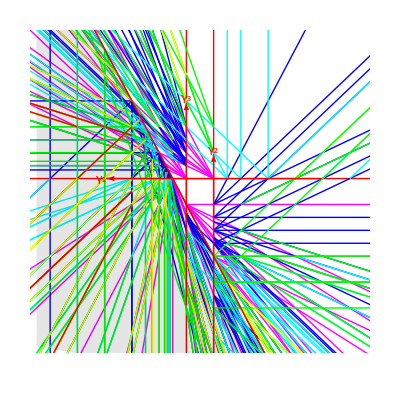

```mathematica
Gr=With[{L=3,m=1/2},Show[Graphics[Table[{Hue[1-(ListRaysI[[k,7]]-1)/6],McKayRay[ListRaysI[[k,1]],ListRaysI[[k,2]],{0,25},""]},{k,Length[ListRaysI]}]],McKayInitialRays[1.95,m],Graphics[{Opacity[.1],Polygon[{InitialRaysOrigin[1/2][[4]]-2McKayVec[{0,0,0,1}],InitialRaysOrigin[1/2][[4]]+2McKayVec[{0,0,0,1}],{-L,-L},{-L,L}}]}],PlotRange->{{-L,L},{-L,L}}]]
```

{{2 γ_2,{γ_3,γ_4}}}

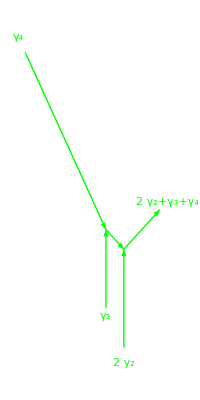

-y+O[1/y]^1

```mathematica
(* find scattering sequences corresponding to given dimension vector *)
With[{Nvec={0,2,1,1},m=1/2},
LiTrees=McKayTreesFromListRays[ListRaysI,Nvec,m];
Print[LiTrees/.McKayrep];
Print[McKayScattDiag[LiTrees,m]];
Index=McKayScattIndex[LiTrees];
Plus@@Series[EvaluateKronecker[Index],{y,Infinity,0}]
]
```

### Figure 30

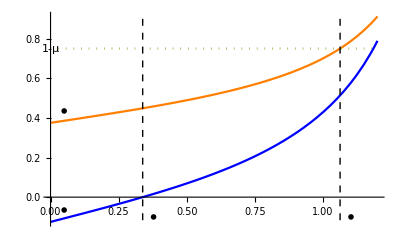

```mathematica
With[{m=1/4+0 I/2},Show[Plot[{
Re[Exp[-I psi](I QuantumVolume[m])]/Cos[psi],
Re[Exp[-I psi](I QuantumVolumep[m])]/Cos[psi],Re[Exp[-I psi](1-m)]/Cos[psi]},{psi,0,1.2},PlotStyle->{Blue, Orange,Dotted}],Graphics[{Dashed,Line[{{CriticalPsi[m][[1,2]],-.5},{CriticalPsi[m][[1,2]],1}}],Line[{{CriticalPsi[m][[2,2]],-.5},{CriticalPsi[m][[2,2]],1}}],Text["1-μ",{0,1-Re[m]}],Text[MaTeX["\\psi^+_{cr}"],{CriticalPsi[m][[1,2]]+.04,-.1}],
Text[MaTeX["\\tilde{\\psi}^+_{cr}"],{CriticalPsi[m][[2,2]]+.04,-.1}],
Text[MaTeX["{\\cal V}_\\psi"],{.05,.06-Im[QuantumVolume[m]]}],
Text[MaTeX["\\tilde{\\cal{ V}}_\\psi"],{.05,.06-Im[QuantumVolumep[m]]}]
}]]]
```